```mathematica
spring - damper system that takes moving average of sample times.
```

Note. We give the received time values the name ' xin' to avoid confusion with actual system time t. The filter ouptut is called 'x'.

There is noise on the wrap time found in the USB packets. The job here is to filter out the noise

### sample times. Each time is time wrap was reported. grep notifyWrap /var/log/system.log | awk ' // { print $7 "," }'

```mathematica
xin={74746457785240,74746643692358,74746829692680,74747014691007,74747200693112,74747386695810,74747572692822,74747757701858,74747943695089,74748129694523,74748315692408,74748500713981,74748686695706,74748872692798,74749058692438,74749243695209,74749429698523,74749615695613,74749801693039,74749986695406,74750172693475,74750358728264,74750544720593,74750730714210,74750915692295,74751101692881,74751287692215,74751473701797,74751658716142,74751844726220,74752030717347,74752216692522,74752401692864,74752587706521,74752773708934,74752959722023,74753145695210,74753330688138,74753516711766,74753702692296,74753888729090,74754073692100,74754259692642,74754445716320,74754631724415,74754816693243,74755002692459,74755188692681,74755374710979,74755559687696,74755745706808,74755931711069,74756117729617,74756303717412,74756488730150,74756674715891,74756860714044,74757046695337,74757231688180,74757417705985,74757603723029,74757789710077,74757974725953,74758160693035,74758346707805,74758532716327,74758718688150,74758903706808,74759089693015,74759275694718,74759461695133,74759646688248,74759832700727,74760018707253,74760204707110,74760389693093,74760575692303,74760761725002,74760947728464,74761133692734,74761318737362,74761504695458,74761690730831,74761876692582,74762061732874,74762247745875,74762433725974,74762619704675,74762804687924,74762990709547,74763176714806,74763362728744,74763548727815,74763733715457,74763919724731,74764105728283,74764291725844,74764476693496,74764662735239,74764848703478,74765034717407,74765219726987,74765405692534,74765591716637,74765777708394,74765963725309,74766148720673,74766334731780,74766520725789,74766706722802,74766891692911,74767077691764,74767263729806,74767449733618,74767634693060,74767820724524,74768006723536,74768192728664,74768377692499,74768563716593,74768749728056,74768935722713,74769121692815,74769306693126,74769492694615,74769678716527,74769864727385,74770049706971,74770235707696,74770421689527,74770607733326,74770792709941,74770978721970,74771164695545,74771350694382,74771536720015,74771721692801,74771907692207,74772093693712,74772279729052,74772464693060,74772650706803,74772836714578,74773022690042,74773207688058,74773393695001,74773579714333,74773765692609,74773951691012,74774136707127,74774322692440,74774508692253,74774694728369,74774879694228,74775065697615,74775251692726,74775437725148,74775622693377,74775808719894,74775994710105,74776180730992,74776366714531,74776551715836,74776737728850,74776923692060,74777109707362,74777294716919,74777480708011,74777666695993,74777852694087,74778037695751,74778223692929,74778409705077,74778595714274,74778781715798,74778966712001,74779152707151,74779338731378,74779524714821,74779709711019,74779895692938,74780081701721,74780267715970,74780452692814,74780638692363,74780824692789,74781010727551,74781195705390,74781381706468,74781567703738,74781753690501,74781939728715,74782124692570,74782310692660,74782496716840,74782682713668,74782867693454,74783053725850,74783239709855,74783425702030,74783610692469,74783796703828,74783982694550,74784168731816,74784354693044,74784539716486,74784725711375,74784911708528,74785097707240,74785282715149,74785468717465,74785654728484,74785840691377,74786025728170,74786211727569,74786397734145,74786583692568,74786769716213,74786954712817,74787140702489,74787326722254,74787512722456,74787697692434,74787883715320,74788069707762,74788255730099,74788440692119,74788626692643,74788812730093,74788998693029,74789184701924,74789369693053,74789555692969,74789741692419,74789927736150,74790112692964,74790298728954,74790484692420,74790670729083,74790855728852,74791041687910,74791227694609,74791413724199,74791598715054,74791784692205,74791970729034,74792156708062,74792342692208,74792527723783,74792713731968,74792899706294,74793085717667,74793270718530,74793456709457,74793642688274,74793828694755,74794013693576,74794199714003,74794385707029,74794571695014,74794757692749,74794942709512,74795128706839,74795314692295,74795500693096,74795685693280,74795871708293,74796057728874,74796243716369,74796428693004,74796614727326,74796800707433,74796986695817,74797172724812,74797357692318,74797543711608,74797729727481,74797915708638,74798100693698,74798286724641,74798472692449,74798658728744,74798843716360,74799029728896,74799215695334,74799401706688,74799587715784,74799772721765,74799958712580,74800144692554,74800330705594,74800515775241,74800701709820,74800887706753,74801073729520,74801258717509,74801444696771,74801630692897,74801816714975,74802002693099,74802187704409,74802373708816,74802559698408,74802745715273,74802930692783,74803116693630,74803302725183,74803488783799,74803673731393,74803859692840,74804045711742,74804231692380,74804416712793,74804602705788,74804788710805,74804974711628,74805160715934,74805345716137,74805531691386,74805717722070,74805903720691,74806088692957,74806274708975,74806460728928,74806646692516,74806831732115,74807017706927,74807203695584,74807389725236,74807575717307,74807760688298,74807946692911,74808132710380,74808318694691,74808503704896,74808689712116,74808875728719,74809061728517,74809246706897,74809432692287,74809618729070,74809804692980,74809990729597,74810175709126,74810361692406,74810547727386,74810733693430,74810918695774,74811104704220,74811290707412,74811476702438,74811661693896,74811847716334,74812033692414,74812219716477,74812404728141,74812590692826,74812776696064,74812962716804,74813148720442,74813333706603,74813519706415,74813705687887,74813891723163,74814076706815,74814262716328,74814448728938,74814634693096,74814819706807,74815005695742,74815191743855,74815377692685,74815563701832,74815748718169,74815934731256,74816120689531,74816306722980,74816491712943,74816677701914,74816863692864,74817049731657,74817234731487,74817420695019,74817606700629,74817792717823,74817978728549,74818163706255,74818349716476,74818535714994,74818721693341,74818906718491,74819092723210,74819278694239,74819464711945,74819649703974,74819835716398,74820021707887,74820207711760,74820393706835,74820578711055,74820764735977,74820950692421,74821136724937,74821321725774,74821507731654,74821693692718,74821879692571,74822064710262,74822250710113,74822436714294,74822622712689,74822807720922,74822993707018,74823179707596,74823365730961,74823551718678,74823736692522,74823922714837,74824108728914,74824294715617,74824479692563,74824665729885,74824851706845,74825037710154,74825222692409,74825408702581,74825594692301,74825780730328,74825966716993,74826151692924,74826337696209,74826523692807,74826709708091,74826894734364,74827080729028,74827266713315,74827452693273,74827637769825,74827823721469,74828009692395,74828195728337,74828381716481,74828566694474,74828752692129,74828938730180,74829124726762,74829309692766,74829495692782,74829681715855,74829867708530,74830052711855,74830238700619,74830424695685,74830610719918,74830796696751,74830981715086,74831167727421,74831353695808,74831539705853,74831724716854,74831910715167,74832096729246,74832282693117,74832467692431,74832653726599,74832839705303,74833025707573,74833211693646,74833396715996,74833582692453,74833768692489,74833954693055,74834139728576,74834325694701,74834511733722,74834697721839,74834882723570,74835068692412,74835254717123,74835440692477,74835625693251,74835811707022,74835997701023,74836183727637,74836369722829,74836554706905,74836740695966,74836926702563,74837112706982,74837297695014,74837483714846,74837669728105,74837855708004,74838040706829,74838226715984,74838412711601,74838598692430,74838784707327,74838969687873,74839155717565,74839341692186,74839527707041,74839712711656,74839898692732,74840084691948,74840270715212,74840455724307,74840641729497,74840827710020,74841013711339,74841199692544,74841384692662,74841570715981,74841756706930,74841942692450,74842127692630,74842313719540,74842499718018,74842685728614,74842870692765,74843056709946,74843242712837,74843428692459,74843614726026,74843799738591,74843985716206,74844171692758,74844357717492,74844542692620,74844728702019,74844914731756,74845100708317,74845285733440,74845471692386,74845657718108,74845843723945,74846029697099,74846214692120,74846400693975,74846586715996,74846772692301,74846957692375,74847143729519,74847329696432,74847515715988,74847700708964,74847886715701,74848072711172,74848258725747,74848443692817,74848629696523,74848815724638,74849001692765,74849187733683,74849372692253,74849558719774,74849744701825,74849930716198,74850115728646,74850301693573,74850487692167,74850673724030,74850858694060,74851044736405,74851230692459,74851416707159,74851602716883,74851787692587,74851973689033,74852159719939,74852345694808,74852530707107,74852716706928,74852902727805,74853088717041,74853273724035,74853459693108,74853645725465,74853831711729,74854016745067,74854202712472,74854388716605,74854574718666,74854760693123,74854945724764,74855131715328,74855317715610,74855503693129,74855688728349,74855874728441,74856060692971,74856246697189,74856431716086,74856617731863,74856803727629,74856989692645,74857175717564,74857360718293,74857546729163,74857732692717,74857918710098,74858103692825,74858289713878,74858475692283,74858661728034,74858846723739,74859032726450,74859218692596,74859404692991,74859590716025,74859775692547,74859961706962,74860147716225,74860333716427,74860518702940,74860704717915,74860890725434,74861076706973,74861261692735,74861447709741,74861633708222,74861819717020,74862005716525,74862190697233,74862376814510,74862562692362,74862748693028,74862933716182,74863119716976,74863305721854,74863491692879,74863676729446,74863862712938,74864048706570,74864234706479,74864420692412,74864605692385,74864791692369,74864977728514,74865163735902,74865348720257,74865534707082,74865720714305,74865906737221,74866091715907,74866277692903,74866463707438,74866649693849,74866834711092,74867020692317,74867206714224,74867392709043,74867578719502,74867763692403,74867949716498,74868135717141,74868321692621,74868506692841,74868692716389,74868878708976,74869064716617,74869249706852,74869435734581,74869621713325,74869807722452,74869993692692,74870178715900,74870364693238,74870550693064,74870736710430,74870921715445,74871107692702,74871293730619,74871479715347,74871664694838,74871850716154,74872036711996,74872222721594,74872408721049,74872593693896,74872779728512,74872965693273,74873151694386,74873336715459,74873522730125,74873708693096,74873894707220,74874079696617,74874265730032,74874451711178,74874637692586,74874823723672,74875008731779,74875194729864,74875380692413,74875566715903,74875751693321,74875937706901,74876123710621,74876309716991,74876494692486,74876680692472,74876866693076,74877052731331,74877238721457,74877423706883,74877609718485,74877795714507,74877981694057,74878166692960,74878352729751,74878538683499,74878724712079,74878909716516,74879095693030,74879281692899,74879467724296,74879652708352,74879838692619,74880024692532,74880210716511,74880396692489,74880581734904,74880767693099,74880953708649,74881139694568,74881324722892,74881510707046,74881696692528,74881882692183,74882067693060,74882253718688,74882439708479,74882625695377,74882811692262,74882996725735,74883182725504,74883368695393,74883554693220,74883739733367,74883925693457,74884111693061,74884297692566,74884482731844,74884668714563,74884854694999,74885040692466,74885226693045,74885411729049,74885597715893,74885783692188,74885969727889,74886154714850,74886340728448,74886526692916,74886712705643,74886897728915,74887083710843,74887269707472,74887455712219,74887641717693,74887826731392,74888012692270,74888198727979,74888384714502,74888569692570,74888755706661,74888941720813,74889127728701,74889312695387,74889498694017,74889684714482,74889870710444,74890055741393,74890241717123,74890427718904,74890613693745,74890799706955,74890984715230,74891170712755,74891356776369,74891542694292,74891727729471,74891913729303,74892099709279,74892285707146,74892470720622,74892656731165,74892842712052,74893028693737,74893214695697,74893399696276,74893585706961,74893771705534,74893957732313,74894142702234,74894328692556,74894514718420,74894700707181,74894885705479,74895071713809,74895257692391,74895443693492,74895629706893,74895814693238,74896000692701,74896186723187,74896372688293,74896557706688,74896743779675,74896929711242};
```

```mathematica
xin=Drop[xin,-20]; (*end is always a mess *)
```

44 kHz
inputSize= 544 multFactor= 12
new bufferSize = 98304 numSamplesInBuffer = 8192

```mathematica
bufsize=8192;
```

```mathematica
rate=44100;
```

#### Expected time between wraps in ns

```mathematica
Texpected=10^9 bufsize /rate//N
```

1.8576×10^8

## CHECK We may want to skip the first frames is this is happening consistently

#### If we start at the wrong moment, where the timing is off from the main pulse, the filter has to adjust to get into the beat. Apparently the first beats are off the main beat. This makes huge difference in max error/drift after fitlering.

```mathematica
(*xin=Drop[xin,5]; (* test. There seems a hickup in sample 3 *)
```

```mathematica
deltas=10^-6(Drop[xin,1]-Drop[xin,-1]); (*NANOsec*)
```

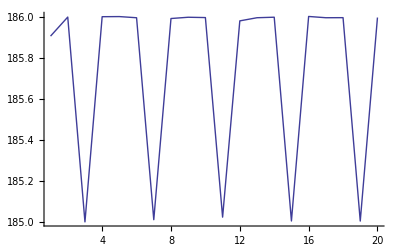

```mathematica
ListPlot[Take[deltas,20],PlotJoined->True,PlotRange->All]
```

```mathematica
(*xin=Take[xin,{200,220}]; (*testing *)
```

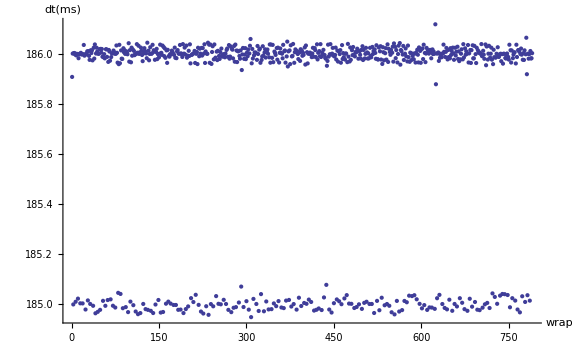

```mathematica
ListPlot[deltas, AxesLabel->{"wrap","dt(ms)"},PlotRange->All]
```

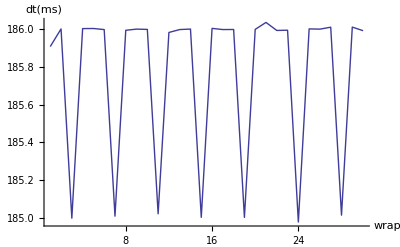

```mathematica
ListPlot[Take[deltas,30], AxesLabel->{"wrap","dt(ms)"},PlotRange->All,PlotJoined->True]
```

```mathematica
NumMeas=10;
```

```mathematica
estimated1=(Plus@@Take[deltas,NumMeas]+1)/NumMeas//N
```

185.891

```mathematica
estimated=Mean[10^-6(Drop[xin,1]-Drop[xin,-1])]//N
```

185.768

Is it close?

```mathematica
(Texpected-10^6 estimated)/Texpected
```

-0.0000463174

#### Init the filter with first sample

```mathematica
x0=xin[[1]]
```

74746457785240

```mathematica
xin=Drop[xin,1]; (* first element was used so do not reuse *)
```

```mathematica
x=x0; (* filtered x *)
u=0; (* u = x-xin : the 'error' is the spring extension *)
dx=Texpected; (* dx/dt = expected change rate of filtered x *)
```

```mathematica
dx=10^6 estimated1
```

1.85891×10^8

```mathematica
xin[[1]]-x
```

185907118

#### Spring constant

```mathematica
K=1;
```

Damping constant

The mass, this determines how slow system follows changes in xin. Bigger=slower.

```mathematica
M=10000;
```

```mathematica
Da=2 √(M K); (*cricital damping *)
```

## Filter

#### Simple filter. This does work in the right direction but lacks damping so lot of overshoot.

```mathematica
filter[inputx_]:=Module[{},
xnext=x+dx;
du=inputx-x;
dx=(99dx+du)/100; (*exponential towards target *)
x=xnext;
x
]
```

#### spring - damper based filter. Is jumpy.

```mathematica
filter[inputx_]:=Module[{},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ; 

x=xnext; u=unext; (* update the filter *)
x
];
```

#### spring - damper filter with outlier check/skip

Works great for the test set. Only worry is that the jitter detect uses the du which is change of error.
  An absolute distance of unext from Texpected might be better but in practice it seems worse

```mathematica
filter[inputx_]:=Module[{xnext, unext, du, F},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ;
x=xnext; u=unext; (* update the filter *)
x
];
```

```mathematica
xfiltered = filter/@xin;
```

```mathematica
10^-6(xfiltered-xin)[[4]]
```

0.642405

### Does it follow xin?

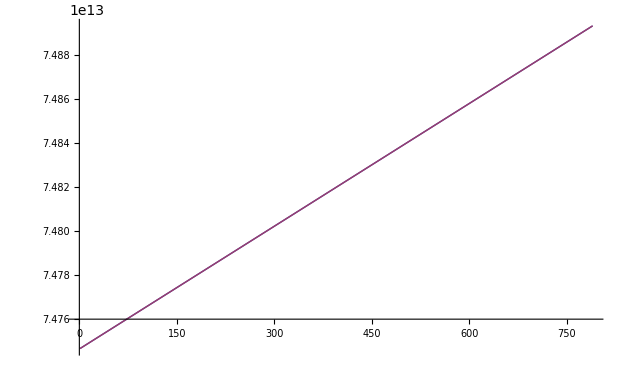

```mathematica
ListPlot[{xfiltered,xin},PlotJoined->True]
```

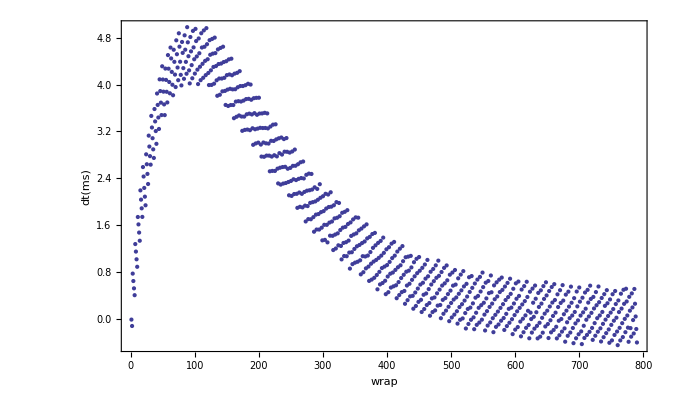

```mathematica
ListPlot[10^-6(xfiltered-xin), FrameLabel->{"wrap","dt(ms)"},PlotRange->All,Frame->True]
```

So the data can come in up to 6 ms late. This is the timestamps straight coming from USB

### Does it keep a solid rate without jumping?

```mathematica
deltas=(Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected;
```

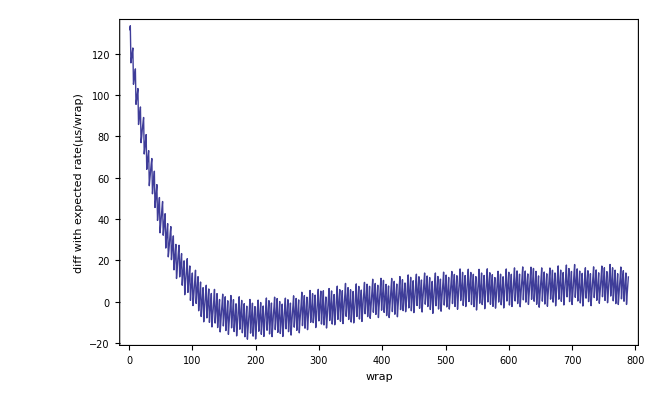

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True,PlotRange->All]
```

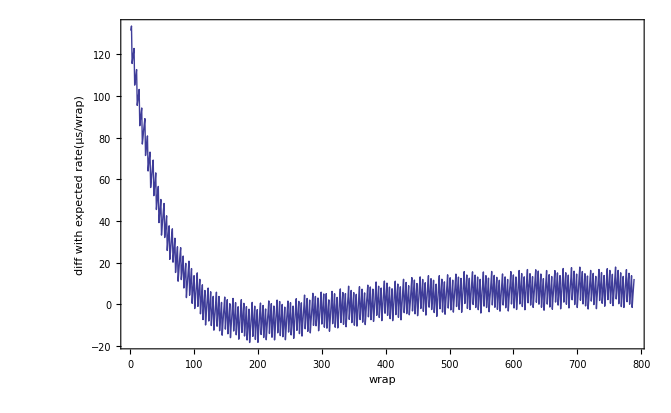

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True,PlotRange->All]
```